## The static magnetic moments μ_I evaluated according to the definition -Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
spins=Table[i/2,{i,47,63,4}];
errplus={0.006,0.005,0.008,0.013,0.012};
errminus={0.005,0.005,0.007,0.011,0.010};
BM1th={0.017,0.018,0.019,0.019,0.020};
BM1exp={0.017,0.017,0.024,0.023,0.024};
A=163;
Z=71;
gR=Z/A;
muI[I_,K_,x_]:=gR*I+x*K^2/(I+1);
diff[BM1_,I_,K_]:=√((4π)/3)(BM1/(K^2*(ClebschGordan[{I,K},{1,0},{I-1,K}])^2))^(1/2);
```

```mathematica
gprimesTh[K_]:=Table[diff[BM1th[[i]],spins[[i]],K],{i,1,Length[BM1th]}];
gprimesExp[K_]:=Table[diff[BM1exp[[i]],spins[[i]],K],{i,1,Length[BM1exp]}];
muITh=Table[{spins[[i]],muI[spins[[i]],spins[[i]]-1,diff[BM1th[[i]],spins[[i]],spins[[i]]-1]]},{i,1,Length[BM1th]}];
muIExp=Table[{spins[[i]],Around[muI[spins[[i]],spins[[i]]-1,diff[BM1exp[[i]],spins[[i]],spins[[i]]-1]],{muI[spins[[i]],spins[[i]]-1,diff[BM1exp[[i]],spins[[i]],spins[[i]]-1]]-muI[spins[[i]],spins[[i]]-1,diff[errminus[[i]],spins[[i]],spins[[i]]-1]],muI[spins[[i]],spins[[i]]-1,diff[BM1exp[[i]],spins[[i]],spins[[i]]-1]]-muI[spins[[i]],spins[[i]]-1,diff[errplus[[i]],spins[[i]],spins[[i]]-1]]}]},{i,1,Length[BM1exp]}];
```

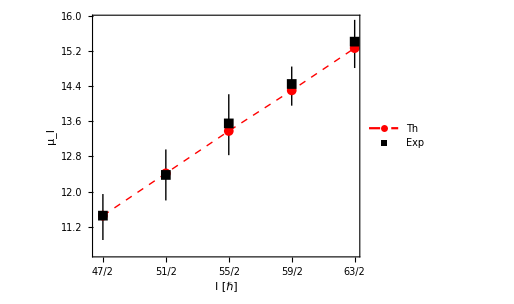

```mathematica
plot=ListPlot[{muITh,muIExp},PlotRange->Full,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,PlotMarkers->{Automatic, Medium},Joined->{True,False},PlotStyle->{{Red,Thick,Dashed},{Black,Thick}},FrameLabel->{"I [ℏ]","μ_I"},LabelStyle->{19,FontFamily->"Times",Black,Bold},FrameTicks->{{Automatic,None},{{47/2,51/2,55/2,59/2,63/2},None}},PlotLegends->Placed[{"Th","Exp"},{0.25,0.8}]];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Quadrupole-Moments/static-muI.pdf",plot];
Show[plot]
```